```mathematica
位置——方向分布
```

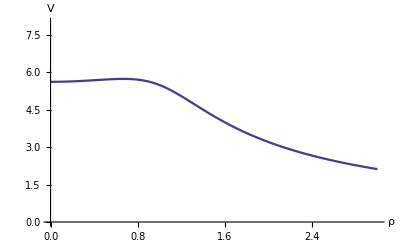

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[z_,ρ_]:=(2 EllipticK[(2 b)/(-a+b)])/(√(a-b))+(2 EllipticK[(2 b)/(a+b)])/(√(a+b));
Plot[V[z,ρ]/.z->R/2,{ρ,0,3*R},
PlotRange->{0,8},AxesLabel->{"ρ","V"},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Clear[R,a,b,V]
```